```mathematica
(* Find an actual line that is perpendicular to the curve at a point with length 1.  its slope should be given by the normal ratio. *)
```

```mathematica
a=3;b=1;
cv = {a Cos[t],b Sin[t]};
outnorm=Assuming[{t>0&&a>0&&b>0},Simplify[{b Cos[t],a Sin[t]}/Sqrt[a^2 Sin[t]^2+b^2 Cos[t]^2]]];
cvout=cv+outnorm;
intgrd = cvout[[1]]^2 D[cvout[[2]],t];
outvol= 2 Pi NIntegrate[intgrd,{t,0,Pi/2},WorkingPrecision->15];
N[outvol-4/3 Pi a a,11]
```

103.37870096

```mathematica
(* Next, let's try to compute the actual integral (with no I's!) *)
```

```mathematica
a=3;b=1;
Clear[a,b]
cv = {a Cos[t],b Sin[t]};
outnorm=Assuming[{t>0&&a>0&&b>0},Simplify[{b Cos[t],a Sin[t]}/Sqrt[a^2 Sin[t]^2+b^2 Cos[t]^2]]];
cvout=cv+outnorm;
intgrdtmp = cvout[[1]]^2 D[cvout[[2]],t];
intgrd=Assuming[{a>0&&b>0&&a>b&&t>0},FullSimplify[intgrdtmp]];
outvol= 2 Pi Assuming[{a>0&&b>0&&a>b},Integrate[intgrd,{t,0,Pi/2}]];
```

```mathematica
simp1=Assuming[{a>0&&b>0&&a>b&&a^2 > b^2},FullSimplify[outvol]];
```

```mathematica
simp1
```

(2 π (((a-b) (a+b))^(7/2) (2+3 b+a^2 (3+2 b))+3 a ((6 a^2 b^6-b^8) ArcCosh[a/b]+a ((a^2-b^2)^3 ArcSec[a/b]-ⅈ a b^2 (a^4-3 a^2 b^2-3 b^4) ArcSec[b/a]))))/(3 ((a-b) (a+b))^(7/2))

```mathematica
simp2=(2 π (((a-b) (a+b))^(7/2) (2+3 b+a^2 (3+2 b))+3 a ((6 a^2 b^6-b^8) ArcCosh[a/b]+a ((a^2-b^2)^3 ArcSec[a/b]-ⅈ a b^2 (a^4-3 a^2 b^2-3 b^4) ArcCos[a/b]))))/(3 ((a-b) (a+b))^(7/2))
```

(2 π (((a-b) (a+b))^(7/2) (2+3 b+a^2 (3+2 b))+3 a ((6 a^2 b^6-b^8) ArcCosh[a/b]+a (-ⅈ a b^2 (a^4-3 a^2 b^2-3 b^4) ArcCos[a/b]+(a^2-b^2)^3 ArcSec[a/b]))))/(3 ((a-b) (a+b))^(7/2))

```mathematica
simp3=(2 π (((a-b) (a+b))^(7/2) (2+3 b+a^2 (3+2 b))+3 a ((6 a^2 b^6-b^8) ArcCosh[a/b]+a ((a^2-b^2)^3 ArcSec[a/b]+a b^2 (a^4-3 a^2 b^2-3 b^4) Log[a/b+ Sqrt[(a^2-b^2)/b^2]]))))/(3 ((a-b) (a+b))^(7/2));
```

```mathematica
N[{simp1,simp3}/.{a->2,b->1},100]
```

{77.10991716519589823137194137518674133933066413975290414903611356223539825939675566416815025921915104,77.10991716519589823137194137518674133933066413975290414903611356223539825939675566416815025921915104}

```mathematica
finans=FullSimplify[simp3-4/3 Pi a^2 b]
```

2/3 π (2+3 a^2+3 b+(3 a ((6 a^2 b^6-b^8) ArcCosh[a/b]+a ((a^2-b^2)^3 ArcSec[a/b]+a b^2 (a^4-3 a^2 b^2-3 b^4) Log[√(-1+a^2/b^2)+a/b])))/((a-b) (a+b))^(7/2))

```mathematica
TeXForm[%73]
```

\frac{2}{3} \pi  \left(3 a^2+\frac{3 a \left(\left(6 a^2
   b^6-b^8\right) \cosh ^{-1}\left(\frac{a}{b}\right)+a
   \left(\left(a^2-b^2\right)^3 \sec
   ^{-1}\left(\frac{a}{b}\right)+a b^2 \left(a^4-3 a^2 b^2-3
   b^4\right) \log
   \left(\sqrt{\frac{a^2}{b^2}-1}+\frac{a}{b}\right)\right)\right)}
   {((a-b) (a+b))^{7/2}}+3 b+2\right)

```mathematica
N[finans/.{a->3,b->1},20]
```

103.37870096022906533

```mathematica
(* Since we assume that a > b, we need to inveert the argument in ArcSec[b/a] in order to get right of the leading I factor.*)
```

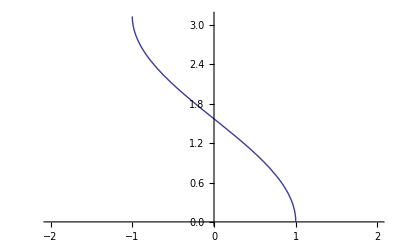

```mathematica
Plot[ArcCos[x],{x,-2,2}]
```